# Visualizing of Quantum Probabilities

## Introduction

This notebook is written at the level for those who are already familiar with the principles of quantum mechanics. In the following cells, we will explore how the solutions to the Schrodinger Equation for a particle in an infinite square well evolve with time. Feel free to use these plots to better understand the underlying physics, e.g. qualitatively interpreting expectation values.

## Frame-By-Frame Time Dependent Probability Density Plots

A particle that experiences a potential energy of the form V(x) = 0 for x∈ [0,L]  and V(x) = ∞ otherwise is described by the energy eigenstates, ϕ_n(x) = √2/L×Sin((n π x)/L) , according to the Schrodinger Equation. These are called stationary states. That is, when a particle is a stationary state, it will remain in that state without any dependence on time. Conversely, a particle that is initially in a superposition of stationary states, e.g. ψ (x,t=0)= ϕ_1(x)+ϕ_2(x) , the relative phase obtains a time evolution of the form ψ(x,t) = Σ_n e^((-i E_n t)/ℏ)ϕ(x)= Σ_n e^((-i E_n t)/ℏ)√2/L×Sin(nπx/L). The time evolution is then ψ(x,t) = ψ_1(x)+e^((-i ΔE t)/ℏ)ψ_2(x)= ψ_1(x)+e^(-i ω)ψ_2(x), where ΔE = E_2-E_1, ω = ΔE/ℏ , and the overall phase is dropped. The one dimensional probability density function,  P(x,t) = |ψ(x,t)|^2 , describes the probability of measuring the particle on an interval,  Δx = b-a , such that the probability of finding the particle on that interval is  𝒫_(a≤x≤b) = (∫_a)^b P(x,t)dx. When viewing the plots below, one may gain an intuition for how the expectation value for position changes in time when ψ(t=0) is not an eigenstate.

Figures 1 and 2 plot the probability density of the n=1 and n=2 stationary states for x∈[L/4,3L/4], (a section spanning the middle of the potential well).

Figures 3-5 plot the probability density of a particle that began in a superposition of the n=1 and n=2 energy eigenstates but at a later time (see plots for the evaluated time).

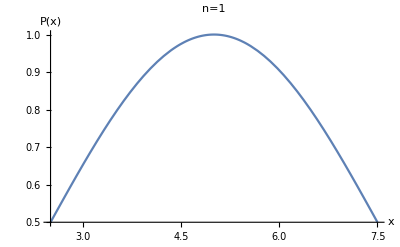

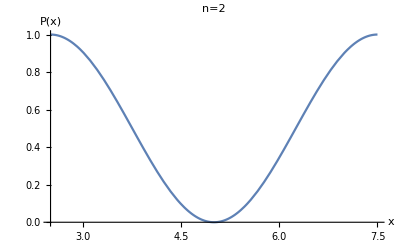

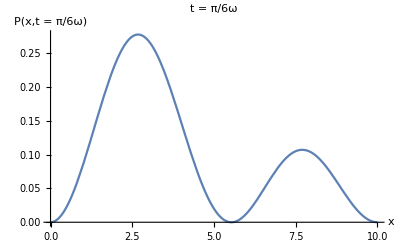

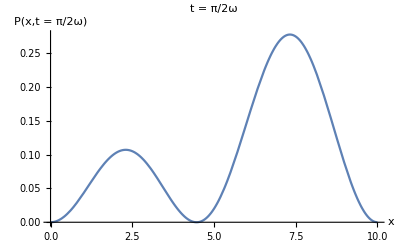

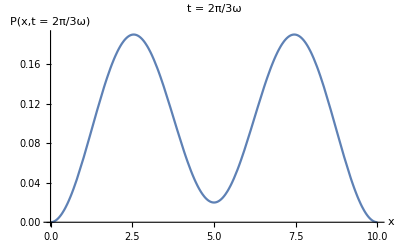

```mathematica
Clear[x,L]
L=10;
w=1;
Plot[(Sin[(Pi*x)/L])^2,{x,L/4,3L/4},PlotLabel->"n=1",AxesLabel->{"x","P(x)"}]
Plot[(Sin[(2Pi*x)/L])^2,{x,L/4,3L/4},PlotLabel->"n=2",AxesLabel->{"x","P(x)"}]
t=Pi/(6w);
Plot[(1/(5*L))*((Sin[Pi*x/L])^2+9(Sin[2*Pi*x/L])^2+6Sin[Pi*x/L]Sin[2*Pi*x/L]Sin[3w*t]),{x,0,L}, PlotLabel-> "t = π/6ω",AxesLabel->{"x","P(x,t = π/6ω)"}]
Clear[x,t]
t=Pi/(2w);
Plot[(1/(5*L))*((Sin[Pi*x/L])^2+9(Sin[2*Pi*x/L])^2+6Sin[Pi*x/L]Sin[2*Pi*x/L]Sin[3w*t]),{x,0,L}, PlotLabel-> "t = π/2ω",AxesLabel->{"x","P(x,t = π/2ω)"}]
Clear[x,t]
t=2*Pi/(3w);
Plot[(1/(5*L))*((Sin[Pi*x/L])^2+9(Sin[2*Pi*x/L])^2+6Sin[Pi*x/L]Sin[2*Pi*x/L]Sin[3w*t]),{x,0,L}, PlotLabel-> "t = 2π/3ω",AxesLabel->{"x","P(x,t = 2π/3ω)"}]
Clear[x,L,w,t]
probability = Integrate[x((1/(5*L))*((Sin[Pi*x/L])^2+9(Sin[2*Pi*x/L])^2+6Sin[Pi*x/L]Sin[2*Pi*x/L]Sin[3w*t])),{x,0,L}];
```

## Time Evolution of Particle in an Infinite Square Potential Well

```mathematica
ClearAll;
Len=1;
w=1;
Animate[Plot[(1/(5*Len))*((Sin[Pi*x/Len])^2+9(Sin[2*Pi*x/Len])^2+6Sin[Pi*x/Len]Sin[2*Pi*x/Len]Sin[3w*time]),{x,0,Len}, PlotLabel-> "t = 0 to t = 2Pi/3ω",PlotRange->{{0,1},{0,3}},AxesLabel->{"x","P(x,t)"}],{time,0,2Pi/3}]
```